```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*INIITIALIZE PARAMETERS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

alpha = 0.5;
beta = 1.0;
delta = 0.5;
katta =5;
qAvg = 1.0;
eta = 0.25;
etaBar = 0.5;
chi = 0.1;
uBar = 1.0;

(*------------------------------------------------------------------------------------------------------------------------------*)
(*AGENTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Number of firms*)
n = 10.0;
(*A dummy vector used to identify each firm by a certain number: 1- first firm, 2-second firm,.....n- nth firm*)
Id = Table[i,{i,1,n}];
(*Number of consumers*)
m= 100.0;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PRICING*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*market share of the specialized firm*)
ms[q0_, qi_]:= q0 / Total[qi];
(*markup smart components*)
etaSpec[delta_, etaSpecLag_, q0_, qi_, etaBar_]:=(1-delta)*etaSpecLag + delta*ms[q0,qi]*etaBar;
(*price of specialist*)
pSpec[cs_,etaSpec_]:=(1+etaSpec)*cs;
(*price of firm if it produces the smart component*)
pFirmSelf[cSelf_,eta_]:=(1+eta)*cSelf;
(*price of firm if it produces the smart component*)
pFirmSpec[cSpec_,eta_]:=(1+eta)*cSpec;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*MARGINAL COSTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Marginal costs of the "usual" component*)
cp = 20.0;
(*Marginal costs of the smart component*)
cs = 10.0;
(*Marginal costs if firm buys smart component from specialist*)
cSelf[cp_, cs_]:=cp + cs;
(*Marginal cost if firm buys smart component from specialist*)
cSpec[cp_,cs_, etaSpec_]:=cp + (1+etaSpec)*cs;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PROFIT*)
(*------------------------------------------------------------------------------------------------------------------------------*)
profit[q_,p_,c_]:=q*p - c*q;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*QUALITY*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*quality of specialist*)
qualitySpec[uBar_, alpha_, beta_,qSpec_ ] :=uBar*(1+ beta*qSpec^alpha);
(*quality of firm*)
qualityFirm[uBar_, alpha_, beta_,qFirm_ ] :=uBar*(1+ beta*qFirm^alpha);
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PROBABILITY*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*A function that computes the probability that consumer j buys from firm i*)
probability[i_,priceList_, qualityList_]:=Module[
{p =priceList, u = qualityList},
Exp[-chi*p[[i]]+ katta*u[[i]]]/Sum[Exp[-chi*p[[k]]+ katta*u[[k]]],{k,1,n}]];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------ EXERCISE 1 a) -------------------------------------------------------------*)
(*---------------------------------(*FIXED STRATEGIES: FIRMS PRODUCE SMART COMPONENT*)------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*Batch Runs*)
(*------------------------------------------------------------------------------------------------------------------------------*)

R=20;
T = 100; (*100*)
count = 0;

Do[
count = count + 1;
(*Store Results in Lists such that 
e.g. priceList[[1,2]] gives the price of the second firm in period 1!!*)

(*prices*)
priceList =Table[Table[0.0,{i,1,n}],{i,1,T}];
qualityList =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*Quantities produced*)
quantPeriod =Table[Table[0.0,{i,1,n}],{i,1,T}];
quantAgg=Table[Table[0.0,{i,1,n}],{i,1,T}]; (*aggregated output*)
(*Profits*)
profitList =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*List of probabilities*)
probList =Table[Table[0.0,{i,1,n}],{i,1,T}];

(*PERIODS*)
Do[
(*compute prices*)
priceList[[t]] =Table[pFirmSelf[cSelf[cp,cs],eta],{i,1,n}];
(*compute aggregated output: depends on aggregate output and period output of LAST PERIOD*)
If[t==1,
quantAgg[[t]]=Table[0.0,{i,1,n}],
quantAgg[[t]]=Table[quantAgg[[t-1,i]]+ quantPeriod[[t-1,i]],{i,1,n}]];
(*compute quality using aggregated output*)
qualityList[[t]] =Table[qualityFirm[uBar, alpha, beta,quantAgg[[t,i]]],{i,1,n}];
(*Compute the probabilities and append them to a list! 
Since each consumer computes these probabilities the same way 
it is necessary to compute them for only one consumer*)
probList[[t]] = Table[probability[i,priceList[[t]], qualityList[[t]]],{i,1,n}];
(*compute demand*)
choiceListAll = RandomChoice[probList[[t]] ->Id,m];
(*Compute quantities produced in period t*)
quantPeriod[[t]] = Table[Count[choiceListAll,i],{i,1,n}];
(*compute profits*)
profitList[[t]] =Table[profit[quantPeriod[[t,i]],priceList[[t,i]],cSelf[cp,cs]],{i,1,n}],

{t,1,T}
];
,{r,1,R}]

(*------------------------------------------------------------------------------------------------------------------------------*)
(*Results*)
(*------------------------------------------------------------------------------------------------------------------------------*)
(*Print["Period Quantities: ", TableForm[quantPeriod]]
Print["Prices: ",TableForm[priceList]]
Print["Qualities: ",TableForm[qualityList]]
Print["Agg. Quantities: ",TableForm[quantAgg]]
Print["Profits: ",TableForm[profitList]]
Print["Probs: ",TableForm[probList]]*)
```

```mathematica
count
```

20

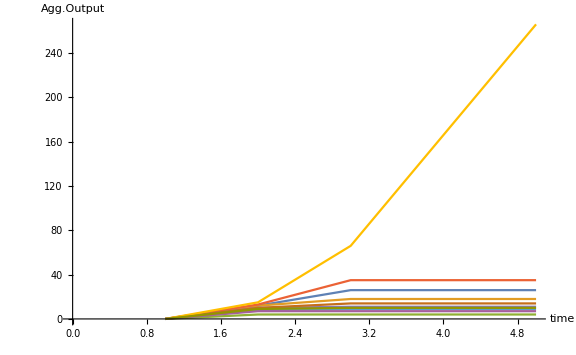

```mathematica
ListPlot[Table[Table[quantAgg[[t,j]],{t,1,5}],{j,1,n}],PlotRange->All,Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Agg.Output]}]
```

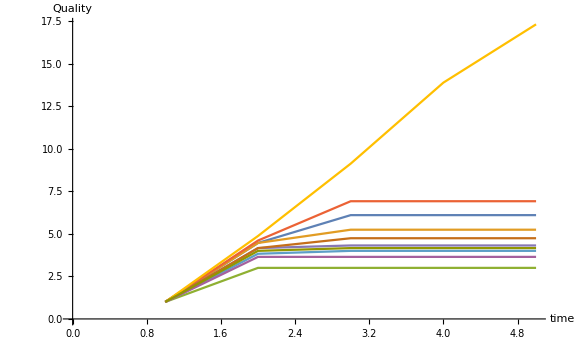

```mathematica
ListPlot[Table[Table[qualityList[[t,j]],{t,1,5}],{j,1,n}],PlotRange->All,Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Quality]}]
```